```mathematica
ClearAll[f];
f[x_]:=Sin[5x];
"f[x] = "<>ToString[f[x],TraditionalForm]
```

f[x] = TraditionalForm`sin(5\ x)

```mathematica
legendre coefficients[func_,n_]:=Do[Print[ToString[Limit[(LegendreP[i,func]/.{Plus->List}),x->1]*Max[Denominator[LegendreP[i,func]]],TraditionalForm]],{i,0,n,1}];
"legendre coefficients[x,10]"
legendre coefficients[x,10]
"legendre coefficients[f[x],10]"
legendre coefficients[f[x],10]
```

legendre coefficients[x,10]

TraditionalForm`1

TraditionalForm`1

TraditionalForm`{-1, 3}

TraditionalForm`{-3, 5}

TraditionalForm`{3, -30, 35}

TraditionalForm`{15, -70, 63}

TraditionalForm`{-5, 105, -315, 231}

TraditionalForm`{-35, 315, -693, 429}

TraditionalForm`{35, -1260, 6930, -12012, 6435}

TraditionalForm`{315, -4620, 18018, -25740, 12155}

TraditionalForm`{-63, 3465, -30030, 90090, -109395, 46189}

legendre coefficients[f[x],10]

TraditionalForm`1

TraditionalForm`sin(5)

TraditionalForm`{-1, 3\ sin^2(5)}

TraditionalForm`{-3\ sin(5), 5\ sin^3(5)}

TraditionalForm`{3, -30\ sin^2(5), 35\ sin^4(5)}

TraditionalForm`{15\ sin(5), -70\ sin^3(5), 63\ sin^5(5)}

TraditionalForm`{-5, 105\ sin^2(5), -315\ sin^4(5), 231\ sin^6(5)}

TraditionalForm`{-35\ sin(5), 315\ sin^3(5), -693\ sin^5(5), 429\ sin^7(5)}

TraditionalForm`{35, -1260\ sin^2(5), 6930\ sin^4(5), -12012\ sin^6(5), 6435\ sin^8(5)}

TraditionalForm`{315\ sin(5), -4620\ sin^3(5), 18018\ sin^5(5), -25740\ sin^7(5), 12155\ sin^9(5)}

TraditionalForm`{-63, 3465\ sin^2(5), -30030\ sin^4(5), 90090\ sin^6(5), -109395\ sin^8(5), 46189\ sin^10(5)}

legendre sum 1[x] = TraditionalForm`sin(5\ x) + 1

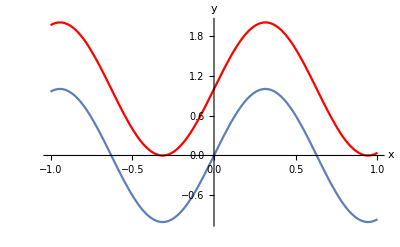

legendre sum 5[x] = TraditionalForm`1/2\ (5\ sin^3(5\ x) - 3\ sin(5\ x)) + 1/2\ (3\ sin^2(5\ x) - 1) + 1/8\ (63\ sin^5(5\ x) - 70\ sin^3(5\ x) + 15\ sin(5\ x)) + 1/8\ (35\ sin^4(5\ x) - 30\ sin^2(5\ x) + 3) + sin(5\ x) + 1

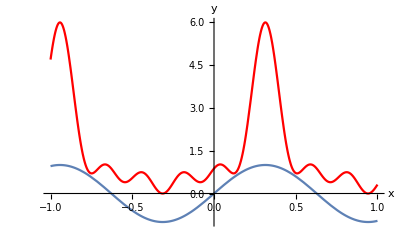

legendre sum 10[x] = TraditionalForm`1/2\ (5\ sin^3(5\ x) - 3\ sin(5\ x)) + 1/2\ (3\ sin^2(5\ x) - 1) + 1/8\ (63\ sin^5(5\ x) - 70\ sin^3(5\ x) + 15\ sin(5\ x)) + 1/8\ (35\ sin^4(5\ x) - 30\ sin^2(5\ x) + 3) + 1/16\ (429\ sin^7(5\ x) - 693\ sin^5(5\ x) + 315\ sin^3(5\ x) - 35\ sin(5\ x)) + 1/16\ (231\ sin^6(5\ x) - 315\ sin^4(5\ x) + 105\ sin^2(5\ x) - 5) + 1/128\ (12155\ sin^9(5\ x) - 25740\ sin^7(5\ x) + 18018\ sin^5(5\ x) - 4620\ sin^3(5\ x) + 315\ sin(5\ x)) + 1/128\ (6435\ sin^8(5\ x) - 12012\ sin^6(5\ x) + 6930\ sin^4(5\ x) - 1260\ sin^2(5\ x) + 35) + 1/256\ (46189\ sin^10(5\ x) - 109395\ sin^8(5\ x) + 90090\ sin^6(5\ x) - 30030\ sin^4(5\ x) + 3465\ sin^2(5\ x) - 63) + sin(5\ x) + 1

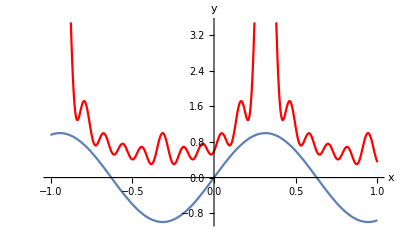

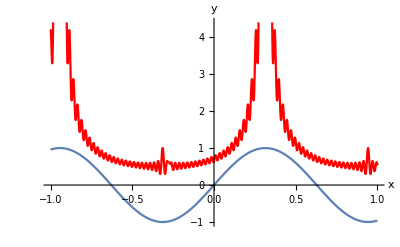

```mathematica
ClearAll[legendre sum];  ClearAll[f graph];  ClearAll[x];
ClearAll[legendre sum 1];  ClearAll[legendre sum 5];  ClearAll[legendre sum 10];
ClearAll[legendre sum 1 graph];  ClearAll[legendre sum 5 graph];  ClearAll[legendre sum 10 graph];

legendre sum[func_,n_]:=Sum[LegendreP[i,func],{i,0,n}];

f graph=Plot[f[x],{x,-1,1}];
legendre sum 1[x_]:=legendre sum[f[x],1];  (* N4a *)
"legendre sum 1[x] = "<>ToString[legendre sum 1[x],TraditionalForm]
legendre sum 1 graph=Plot[legendre sum 1[x],{x,-1,1},PlotStyle->Red];
Show[f graph,legendre sum 1 graph,PlotRange->Automatic,AxesLabel->{"x","y"}]

legendre sum 5[x_]:=legendre sum[f[x],5];  (* N4b *)
"legendre sum 5[x] = "<>ToString[legendre sum 5[x],TraditionalForm]
legendre sum 5 graph=Plot[legendre sum 5[x],{x,-1,1},PlotStyle->Red];
Show[f graph,legendre sum 5 graph,PlotRange->Automatic,AxesLabel->{"x","y"}]

legendre sum 10[x_]:=legendre sum[f[x],10];  (* N4c *)
"legendre sum 10[x] = "<>ToString[legendre sum 10[x],TraditionalForm]
legendre sum 10 graph=Plot[legendre sum 10[x],{x,-1,1},PlotStyle->Red];
Show[f graph,legendre sum 10 graph,PlotRange->Automatic,AxesLabel->{"x","y"}]

legendre sum 50[x_]:=legendre sum[f[x],50];
(* "legendre sum 50[x] = "<>ToString[legendre sum 50[x],TraditionalForm] *)
legendre sum 50 graph=Plot[legendre sum 50[x],{x,-1,1},PlotStyle->Red];
Show[f graph,legendre sum 50 graph,PlotRange->Automatic,AxesLabel->{"x","y"}]
```